```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"];
SetDirectory[NotebookDirectory[]];
paramList=Import["paramList.csv"][[1]]; 
images=Import["Images.csv"];
imgsize=Length[images];(*actual size of imported images*)
```

set image ROI

```mathematica
imgsize2={{1,imgsize-1},{1,imgsize-1}};

{{8,imgsize-4},{6,imgsize-5}};{{13,18},{14,20}}; (*cropped size of images*)
nImages=Length[images[[1]]]/(imgsize );
img[n_]:=images[[;;,imgsize(n-1)+1;;n imgsize-1]][[imgsize2[[1,1]];;imgsize2[[1,2]],imgsize2[[2,1]];;imgsize2[[2,2]]]];
(*loading images*)
listNa=Range[1,nImages,4];
listCs=Range[2,nImages,4];

(*surviving images*)
listNa2=Range[3,nImages,4];
listCs2=Range[4,nImages,4];

maxrangeNa=Max[Flatten[img[#]&/@listNa]];
maxrangeCs=Max[Flatten[img[#]&/@listCs]];
(*sum*)
{xOffsNa,yOffsNa}={12,2};
{xOffsCs,yOffsCs}={8,4};
GraphicsGrid[{{Show[{ArrayPlot[Total[img[#]&/@listCs]],
Graphics[{{Transparent,EdgeForm[Directive[Thick,Dashed,Blue]],Rectangle[{xOffsCs,yOffsCs},{xOffsCs+3,yOffsCs+3}]},{Transparent,EdgeForm[Directive[Thick,Dashed,Orange]],Rectangle[{xOffsNa,yOffsNa},{xOffsNa+3,yOffsNa+3}]}}]
}],

Show[{ArrayPlot[Total[img[#]&/@listNa]],
Graphics[{{Transparent,EdgeForm[Directive[Thick,Dashed,Blue]],Rectangle[{xOffsCs,yOffsCs},{xOffsCs+3,yOffsCs+3}]},{Transparent,EdgeForm[Directive[Thick,Dashed,Orange]],Rectangle[{xOffsNa,yOffsNa},{xOffsNa+3,yOffsNa+3}]}}]
}]}}]

imgROI[n_,xOffs_,yOffs_]:=img[n][[-(yOffs+3);;-(yOffs+1),xOffs+1;;xOffs+3]];
GraphicsGrid[{{ArrayPlot[Total[imgROI[#,xOffsCs,yOffsCs]&/@listCs]],
ArrayPlot[Total[imgROI[#,xOffsNa,yOffsNa]&/@listNa]]}}]
```

set threshold

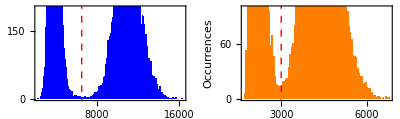

```mathematica
(*load totals*)
NaTotals=Total[Total[imgROI[#,xOffsNa,yOffsNa]]]&/@listNa;
CsTotals=Total[Total[imgROI[#,xOffsCs,yOffsCs]]]&/@listCs;

(*survival totals*)
NaTotals2=Total[Total[imgROI[#,xOffsNa,yOffsNa]]]&/@listNa2;
CsTotals2=Total[Total[imgROI[#,xOffsCs,yOffsCs]]]&/@listCs2;

threshCs=6500;
threshNa=3000;
Loads=Thread[{Boole[#>threshCs&/@CsTotals],Boole[#>threshNa&/@NaTotals]}];

Survs=Thread[{Boole[#>threshCs&/@CsTotals2],Boole[#>threshNa&/@NaTotals2]}];
scale=1;
GraphicsRow[{Show[{
Histogram[CsTotals/scale,100,Frame->True,Axes->False,ChartStyle->Blue,LabelStyle->{Black,Medium},FrameLabel->{"Photoelectron counts ("<>ToString[scale]<>")","Occurrences"},FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{All,{0,200}}],
Graphics[{Red,Dashed,Thick,InfiniteLine[{{threshCs/scale,0} ,{threshCs/scale,1}}]}]
}],
Show[{Histogram[NaTotals/scale,100,Frame->True,Axes->False,ChartStyle->Orange,LabelStyle->{Black,Medium},FrameLabel->{"Photoelectron counts ("<>ToString[scale]<>")","Occurrences"},FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{All,{0,100}}],
Graphics[{Red,Dashed,Thick,InfiniteLine[{{threshNa/scale,0} ,{threshNa/scale,1}}]}]}]
},ImageSize->400]
```

set cases for data plot

```mathematica
data=SortBy[Thread[{paramList, Loads, Survs}],First];
(*caseLoad ={x,y}; caseSurv={{x1,y1},{x2,y2},...}(ie has to be in list form)*)
dataCases[caseLoad0_,caseSurv0_]:=Module[{caseLoad=caseLoad0,caseSurv=caseSurv0},
WilsonInt[n_,p_,z_]:={1/(1+1/n z^2)(p+1/(2n)z^2-z √(1/n p(1-p)+1/(4 n^2 z^2))),1/(1+1/n z^2)(p+1/(2n)z^2+z √(1/n p(1-p)+1/(4 n^2 z^2)))};
datLoadCase=GroupBy[Cases[data,x_/;x[[2]]==caseLoad],First];
datSurvCase=GroupBy[Cases[data,x_/;x[[2]]==caseLoad&&MemberQ[caseSurv,x[[3]]]],First];

params=Union[paramList];
(*preserve order of params*)
nLoads=Key[#][(Length[#]&/@datLoadCase)]&/@params;
nSurvs=Key[#][(Length[#]&/@datSurvCase)]&/@params;
nSurvs=Boole[NumberQ[#]]#&/@nSurvs;

wilsonInts=1.WilsonInt[nLoads[[#]],nSurvs[[#]]/nLoads[[#]],1]&/@Range[Length[nLoads]];
pSurvs=Mean[#]&/@wilsonInts;
errors=Flatten[Differences[#]&/@wilsonInts]/2;

Thread[{Thread[{params,pSurvs}],ErrorBar[#]&/@errors}]
]
```

```mathematica
(*two body version*)
τ2bodyLowHF=1000 0.6218543387267211;
τ1body=5264.5;(*in ms*)
(*getFit[data0_,oneBodyQ0_]:=Module[{data=data0,oneBodyQ=oneBodyQ0},
errs=Quiet[Cases[ToExpression[StringSplit[ToString[data[[;;,2]]],{"ErrorBar[","]"}]],x_/;Head[x]==Real]];
If[oneBodyQ,
fitfn=CC Exp[ -t/τ1body],
fitfn=1-(A Exp[-t/τ]+B Exp[ -t/τ2bodyLowHF]+CC Exp[ -t/τ1body])
];
nlm=NonlinearModelFit[data[[;;,1]],fitfn,{{A,.34},{τ,12},{tOffs,-2},{B,.17},{CC,0.001}},t,Weights->1/errs]
];*)

getFit[data0_,nBodies0_]:=Module[{data=data0,nBodies=nBodies0},
errs=Quiet[Cases[ToExpression[StringSplit[ToString[data[[;;,2]]],{"ErrorBar[","]"}]],x_/;Head[x]==Real]];

Switch[nBodies,
1,
fitfn=(A Exp[-t/τ]+B Exp[ -t/τ2bodyLowHF]+CC Exp[ -t/τ1body]),
0,
fitfn=1-(A Exp[-t/τ]+B Exp[ -t/τ2bodyLowHF]+CC Exp[ -t/τ1body]),
2,
fitfn=(A Exp[-t/τ]+B Exp[ -t/τ2bodyLowHF]+CC Exp[ -t/τ1body])
];
nlm=NonlinearModelFit[data[[;;,1]],fitfn,{{A,.34},{τ,12},{tOffs,-2},{B,.17},{CC,0.001}},t,Weights->1/errs]
];
```

```mathematica
listplot={{0,1},{1,0},{1,1},{0,0}};

datas=Reap[
Do[

datai=dataCases[{1,1},{i}];
nlmi=getFit[datai,Total[i]];
Sow[{datai,nlmi[t],nlmi}];
,{i,listplot}]
][[2,1]];
```

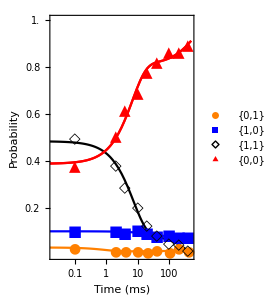

```mathematica
Show[{
LogLinearPlot[{
datas[[1,2]],
datas[[2,2]],
datas[[3,2]],
datas[[4,2]]

},{t,0.01,500},PlotStyle->{{Orange,Thin},{Blue,Thin},{Black,Thin},{Red,Thick}},PlotRange->{{.02,500},{0,1}},Axes->False,Frame->True,FrameLabel->{"Time (ms)","Probability"},LabelStyle->{Black,17}
,FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{Automatic,None}}
]
, 
ErrorListLogLinearPlot[datas[[;;,1]],PlotLegends->{"{0,1}","{1,0}","{1,1}","{0,0}"}, PlotMarkers->{
{Graphics`PlotMarkers[][[1,1]],14},
{Graphics`PlotMarkers[][[2,1]],15},
{Graphics`PlotMarkers[][[8,1]],15},
{Graphics`PlotMarkers[][[4,1]],15}
},
PlotStyle->{{Orange,Thin},{Blue,Thin},{Black,Thin},{Red,Thin}}],

LogLinearPlot[{
datas[[4,2]]
},{t,0.01,500},PlotStyle->{{Red,Thick}},PlotRange->{All,{0,1}}
]

},AspectRatio->1.5,ImageSize->220/1.07]
```

```mathematica
Export["mixedHF.pdf",%]
```

mixedHF.pdf

# inspect fit params

```mathematica
i=4;
Thread[{
Join[{"Cs,Na=",datas[[i,3]]["BestFitParameters"]}]
,Join[{ToString[listplot[[i]]],datas[[i,3]]["ParameterErrors"]}]
}]//TableForm

datas[[i,3]][Infinity]
datas[[i,3]][0]
```

Cs,Na= | {0, 0}
A→0.421953
τ→6.80466
tOffs→-2.
B→0.183373
CC→0.007041 | 0.0323392
1.3747
7.63634×10^-17
0.0876449
0.0706714

1.

0.387633

## save

Cs,Na= | {1, 1}
offs→1.
A→-0.395058
τ→7.07283
tOffs→-2.
B→-0.34861
CC→1.25863 | 1.94523×10^-14
0.0294499
1.35906
0.
0.0632935
0.0492338

1.

0.485035